```mathematica
CircleDot[a_,b_]:=a+b;
CirclePlus[a_,b_]:=Min[a,b];
```

```mathematica
MyMatrixMultiplication[A_,B_]:=Module[{p,q1,q2,r,index1,index2,index3,output},
{p,q1}=Dimensions[A];
{q2,r}=Dimensions[B];
If[q1≠q2,output=0;Abort[]];
output=ConstantArray[30000,{p,r}];
For[index1=1,index1≤p,index1++,
For[index3=1,index3≤r,index3++,
output[[index1]][[index3]]=+400;
For[index2=1,index2≤q1,index2++,
output[[index1]][[index3]]=CirclePlus[output[[index1]][[index3]],CircleDot[A[[index1]][[index2]],B[[index2]][[index3]]]];
];
];
];
output
]
```

```mathematica
A={{3,2},{5,3},{7,3}};
B={{4,2,1},{4,1,5}};
MyMatrixMultiplication[A,B]
```

{{6,3,4},{7,4,6},{7,4,8}}

```mathematica
pol=Unevaluated[Sum[RandomInteger[4]*x^a*y^b*z^c,{a,0,1},{b,0,1},{c,0,1}]];
ideal={pol,pol,pol};
basis1=GroebnerBasis[ideal,{x,y},CoefficientDomain->InexactNumbers];
Print[done1];
basis2=GroebnerBasis[basis1,{x,y},CoefficientDomain->InexactNumbers];
basis3=GroebnerBasis[basis1,{y,x},CoefficientDomain->InexactNumbers];
basis4=GroebnerBasis[basis3,{x,y},CoefficientDomain->InexactNumbers];
basis1===basis4
basis1===basis3
basis1===basis2
```

done1

True

False

True

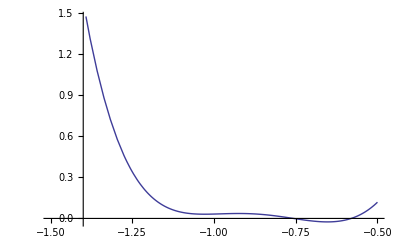

```mathematica
Plot[basis1[[1]],{z,-1.5,-.5}]
```

```mathematica
NSolve[basis1[[1]]==0,z,Reals]
```

{{z→-0.75722694142951422831595355272461643499496102117072368811436612550597041395516009949},{z→-0.580292571223644068607969834956508307837433165470733788919162156012140752975315208206}}